## Week 8

### S17 - Undamped Second-Order Systems S18 - Damped Second-Order Systems

#### Lectures

{{v[t]→V-V Cos[t/(√c √l)]}}

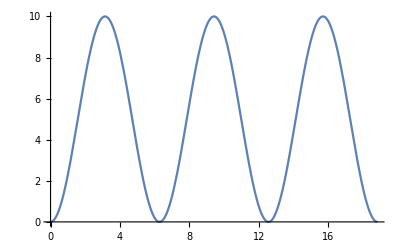

```mathematica
(*Summary of driven LC oscillator*)
DSolve[{l c v''[t]+v[t]==V,v'[0]==0,v[0]==0},v[t],t]
(*Plotting this solution for initial conditions: voltage Subscript[V, I]= 5 V and oscillator frequency Subscript[ω, 0]= 1/√LC= 1*)
Plot[5-5 Cos[t],{t,0,6π}]
```

```mathematica
(*Part 4 solution is repeated (typo)*)
```

```mathematica
(*Now we analyze RLC circuits (damped oscillations)*)
```

```mathematica
(*Summary of driven RLC dampled oscillator*)
DSolve[{l*c*v''[t]+r*c*v'[t]+v[t]==V,v'[0]==0,v[0]==0},v[t],t]
(*Looks different from the total solution derived in lecture, TODO make it look similar, not use hyperbolic fns*)
-1/(2 √(-4 l+c r^2))(-√c ⅇ^(1/2 (-r/l-(√(-4 l+c r^2))/(√c l)) t) r+√c ⅇ^(1/2 (-r/l+(√(-4 l+c r^2))/(√c l)) t) r-2 √(-4 l+c r^2)+ⅇ^(1/2 (-r/l-(√(-4 l+c r^2))/(√c l)) t) √(-4 l+c r^2)+ⅇ^(1/2 (-r/l+(√(-4 l+c r^2))/(√c l)) t) √(-4 l+c r^2)) V//ExpToTrig
```

{{v[t]→-1/(2 √(-4 l+c r^2))(-√c ⅇ^(1/2 (-r/l-(√(-4 l+c r^2))/(√c l)) t) r+√c ⅇ^(1/2 (-r/l+(√(-4 l+c r^2))/(√c l)) t) r-2 √(-4 l+c r^2)+ⅇ^(1/2 (-r/l-(√(-4 l+c r^2))/(√c l)) t) √(-4 l+c r^2)+ⅇ^(1/2 (-r/l+(√(-4 l+c r^2))/(√c l)) t) √(-4 l+c r^2)) V}}

V-1/2 V Cosh[(r t)/(2 l)-(√(-4 l+c r^2) t)/(2 √c l)]-(√c r V Cosh[(r t)/(2 l)-(√(-4 l+c r^2) t)/(2 √c l)])/(2 √(-4 l+c r^2))-1/2 V Cosh[(r t)/(2 l)+(√(-4 l+c r^2) t)/(2 √c l)]+(√c r V Cosh[(r t)/(2 l)+(√(-4 l+c r^2) t)/(2 √c l)])/(2 √(-4 l+c r^2))+1/2 V Sinh[(r t)/(2 l)-(√(-4 l+c r^2) t)/(2 √c l)]+(√c r V Sinh[(r t)/(2 l)-(√(-4 l+c r^2) t)/(2 √c l)])/(2 √(-4 l+c r^2))+1/2 V Sinh[(r t)/(2 l)+(√(-4 l+c r^2) t)/(2 √c l)]-(√c r V Sinh[(r t)/(2 l)+(√(-4 l+c r^2) t)/(2 √c l)])/(2 √(-4 l+c r^2))

```mathematica
(*For some reason the official solution removes the sign in the atan but grader has the correct solution*)
l=10*^-6;c=10*^-12;r=1*^3;
α=r/(2l)
ω0=1/(√(l c))
ωd=√(ω0^2-α^2)//N

VI=3;
ArcTan[-α/ωd]
-VI*(ω0/ωd)
```

50000000

100000000

8.66025×10^7

-0.523599

-3.4641

#### Homework

```mathematica
(*This is more of a theory question. Mathematica can be useless/misleading here*)
l=35;c=11.58*^-3;
Subscript[ω, 0]=1/(√(l c));
f=Subscript[ω, 0]/(2π)

vc[0]=0;il[0]=1;
(*Initially all energy is stored in the inductor*)
1/2 l*il[0]^2
(*Because time period T=4s, and this is an LC oscillator without dissipation, t=9^-s is the exact moment when all energy has sloshed into the capacitor*)
Solve[35/2==1/2 c*v^2,v]
(*At t=9^+s we get a current impulse, remember that capacitor acts like an instantaneous short circuit and inductor acts like an instantaneous open circuit*)
q=2/π;(*Using the rounded value 0.637 gives wrong answer*)
-54.976836070455974+q/c
1/2 c*(-0.0010353478669031801)^2
```

0.249995

35/2

{{v→-54.9768},{v→54.9768}}

-0.00103535

6.20656×10^-9

#### Lab

```mathematica
(*Part 1*)
l=20*^-3;
Solve[2π*100*^3==1/(√(l c)),c]//N
(*Part 2 - Solved with experimentation*)(*Part 3 - Solved with experimentation*)
```

{{c→1.26651×10^-10}}